```mathematica
VT[T_]:=T*0.02585/300
```

```mathematica
ID[n_,J0_,T_,V_]:=J0*(Exp[V/(n*VT[T])]-1)
```

```mathematica
VT[300]
```

0.02585

```mathematica
ID[1.5,1,300,0.1]
```

12.1837

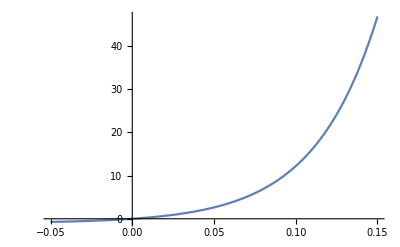

```mathematica
Plot[ID[1.5,1,300,V],{V,-0.05,0.15}]
```

```mathematica
Manipulate[Plot[ID[n,1,T,V],{V,-0.5,0.2}],{n,1,2},{T,100,400}]
```